```mathematica
Clear[allGraphs]
```

```mathematica
colors=1;
```

```mathematica
allGraphs=allGraphs3;
```

```mathematica
allKey=K3Key;
```

```mathematica
SymbolToLabel2[s_]:=Block[{blocks=StringSplit[StringDrop[SymbolName[s ],1],"x"]},
blocks=Select[blocks,StringLength[#]>1&];
If[Length[blocks]==0,
Style[OverHat[1],Darker[Darker[Red]],12]
,
If[StringLength[blocks[[1]]]==nodeCount,
Style[OverHat[0],Darker[Darker[Red]],12]
,
Row[Riffle[blocks ,Style["♁",Darker[Darker[Green]],12]]]
]
]
]
```

```mathematica
fullAtoms=Sort[allGraphs3AtomKeys,CompareSymbols[allGraphs[#1,"colofour"],allGraphs[#2,"colofour"]]&];
```

```mathematica
nullAtoms=Sort[allGraphs3NullAtomKeys,CompareSymbols[allGraphs[#1,"colofourrealnull"],allGraphs[#2,"colofourrealnull"]]&];
```

```mathematica
CompareSymbols[s1_,s2_]:=Block[{str1,str2,c1,c2,p1,p2},
str1=StringDrop[SymbolName[s1],1];
str2=StringDrop[SymbolName[s2],1];
p1=StringToPartition[str1];
p2=StringToPartition[str2];
c1=PartitionFaculty[p1];
c2=PartitionFaculty[p2];
If[c1≠c2,
Less[c1,c2],
str1=StringReplace[str1,"x"->"-"];
str2=StringReplace[str2,"x"->"-"];
AlphabeticOrder[ str1,str2]>0
]
]
```

```mathematica
fullSymbols=Sort[Table[allGraphs[k,"colofour"],{k,fullAtoms}],CompareSymbols];
```

```mathematica
nullSymbols=Sort[Table[allGraphs[k,"colofourrealnull"],{k,nullAtoms}],CompareSymbols];
```

```mathematica
fullVars=Table[Indexed[f,SymbolToLabel2[s]],{s,fullSymbols}];
```

```mathematica
nullVars=Table[Indexed[n,SymbolToLabel2[s]],{s,nullSymbols}];
```

## Start computations

```mathematica
mobius=MobiusMatrix[allGraphs];
```

```mathematica
zeta=Inverse[mobius];
```

```mathematica
NullVector[k_]:=Table[Coefficient[allGraphs[k,"colofourrealnull"],s],{s,nullSymbols }]
```

```mathematica
FullVector[k_]:=Table[Coefficient[allGraphs[k,"colofour"],s],{s,fullSymbols}]
```

```mathematica
Table[NullVector[k],{k,fullAtoms}]//MatrixForm
```

(1 | -1 | -1 | -1 | 2
0 | 1 | 0 | 0 | -1
0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 1)

```mathematica
(*Table[k->NullVector[k].zeta==FullVector[k],{k,Keys[allGraphs]}]*)
```

## Now do some solving

```mathematica
nodeCount=VertexCount[allGraphs[0,"graph"]]
```

3

```mathematica
tailLength=Sum[StirlingS2[nodeCount,k],{k,1,colors}]
```

1

```mathematica
vectorLength=BellB[nodeCount]
```

5

```mathematica
Column[{"^","1"},Spacings->{0,0}]
```

^
1

```mathematica
Table[SymbolToLabel2[ s],{s,fullSymbols}]
```

{OverHat[1],23,12,13,OverHat[0]}

```mathematica
Table[Indexed[f,SymbolToLabel2[ k]],{k,fullSymbols}];
```

```mathematica
fullPositive=Table[Indexed[f,SymbolToLabel2[ k]],{k,Take[fullSymbols,vectorLength-tailLength]}]
```

{fOverHat[1],f23,f12,f13}

```mathematica
fullZero=Table[Indexed[f,SymbolToLabel2[ k]],{k,Take[fullSymbols,-tailLength]}]
```

{fOverHat[0]}

```mathematica
fullVec=Join[fullPositive,Table[0,{k,1,tailLength}]]
```

{fOverHat[1],f23,f12,f13,0}

```mathematica
fullVec2=Table[Indexed[f,SymbolToLabel2[ k]],{k,Take[fullSymbols,vectorLength]}]
```

{fOverHat[1],f23,f12,f13,fOverHat[0]}

```mathematica
nullPositive=Table[Indexed[n,SymbolToLabel2[ k]],{k,Take[fullSymbols,vectorLength-tailLength]}]
```

{nOverHat[1],n23,n12,n13}

```mathematica
nullZero=Table[Indexed[n,SymbolToLabel2[ k]],{k,Take[fullSymbols,-tailLength]}]
```

{nOverHat[0]}

```mathematica
k6VecRep=Table[nullSymbols[[k]]->Sign[NullVector[K6Key][[k]]],{k,vectorLength}]
```

{n1x2x3→0,n1x23→0,n12x3→0,n13x2→0,n123→0}

```mathematica
nullVec=Table[Indexed[n,SymbolToLabel2[ k]](**(k/.k6VecRep)*),{k,nullSymbols}]
```

{nOverHat[1],n23,n12,n13,nOverHat[0]}

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Select[Keys[allGraphs],FullVector[#][[2]]==1&&VertexCount[allGraphs[#,"graph"]]==nodeCount&]}]
```

{-Graphics-0,-Graphics-9,-Graphics-12,-Graphics-3}

```mathematica
Table[Last[FullVector[k]],{k,Select[Keys[allGraphs],VertexCount[allGraphs[#,"graph"]]==nodeCount&]}]//Tally//Sort
```

{{0,7},{1,1}}

```mathematica
ExpressionToTable2[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]],{i,1,Length[exp]}],{i,Length[exp]}]]},
Multicolumn[vals,1]
]
```

```mathematica
Fold[And,Table[0≤Indexed[f,SymbolToLabel2[s]]≤1,{s,fullSymbols}]]
```

0≤fOverHat[1]≤1&&0≤f23≤1&&0≤f12≤1&&0≤f13≤1&&0≤fOverHat[0]≤1

```mathematica
{fullVec,fullVec2}//MatrixForm
```

(fOverHat[1] | f23 | f12 | f13 | 0
fOverHat[1] | f23 | f12 | f13 | fOverHat[0])

```mathematica
Fold[And,RandomSample[With[{all= Reduce[nullVec.mobius==fullVec]},Table[all[[k]],{k,1,Length[all]}]],vectorLength]]
```

f23==n23-nOverHat[1]&&fOverHat[1]==nOverHat[1]&&f12==-n13-n23+nOverHat[0]+nOverHat[1]&&n12==-n13-n23+nOverHat[0]+2 nOverHat[1]&&f13==n13-nOverHat[1]

```mathematica
reduced=Reduce[Fold[And,RandomSample[With[{all= Reduce[nullVec.mobius==fullVec]},Table[all[[k]],{k,1,Length[all]}]],vectorLength]]&&nOverHat[1]==1&&nOverHat[1]==1,nullSymbols];
```

```mathematica
vecs=Table[reduced[[k]],{k,1,vectorLength}]
```

{nOverHat[1]==1,n12==2-n13-n23+nOverHat[0],fOverHat[1]==1,f23==-1+n23,f13==-1+n13}

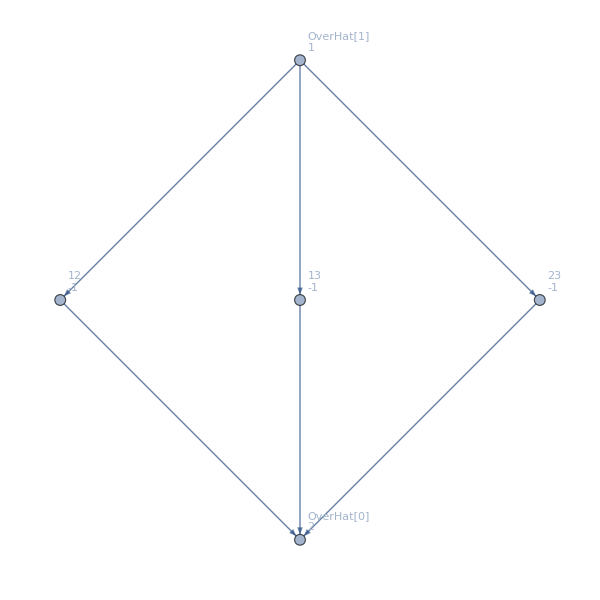

```mathematica
MobiusGraph5[allKey,allGraphs]
```

```mathematica
ExpressionToTable2[reduced]
```

f12==1-n13-n23+nOverHat[0]
f13==-1+n13
f23==-1+n23
fOverHat[1]==1
n12==2-n13-n23+nOverHat[0]
nOverHat[1]==1

```mathematica
ToRules[Reduce[nullVec.zeta==fullVec&&Fold[And,Table[0≤s≤1,{s,fullVars}]],nullVars,Integers]]
```

Sequence[{fOverHat[0]→0,f12→0,f13→0,f23→0,fOverHat[1]→0,nOverHat[1]→0,n23→0,n12→0,n13→0,nOverHat[0]→0},{fOverHat[0]→0,f12→0,f13→0,f23→0,fOverHat[1]→1,nOverHat[1]→1,n23→-1,n12→-1,n13→-1,nOverHat[0]→2},{fOverHat[0]→0,f12→0,f13→0,f23→1,fOverHat[1]→0,nOverHat[1]→0,n23→1,n12→0,n13→0,nOverHat[0]→-1},{fOverHat[0]→0,f12→0,f13→0,f23→1,fOverHat[1]→1,nOverHat[1]→1,n23→0,n12→-1,n13→-1,nOverHat[0]→1},{fOverHat[0]→0,f12→0,f13→1,f23→0,fOverHat[1]→0,nOverHat[1]→0,n23→0,n12→0,n13→1,nOverHat[0]→-1},{fOverHat[0]→0,f12→0,f13→1,f23→0,fOverHat[1]→1,nOverHat[1]→1,n23→-1,n12→-1,n13→0,nOverHat[0]→1},{fOverHat[0]→0,f12→0,f13→1,f23→1,fOverHat[1]→0,nOverHat[1]→0,n23→1,n12→0,n13→1,nOverHat[0]→-2},{fOverHat[0]→0,f12→0,f13→1,f23→1,fOverHat[1]→1,nOverHat[1]→1,n23→0,n12→-1,n13→0,nOverHat[0]→0},{fOverHat[0]→0,f12→1,f13→0,f23→0,fOverHat[1]→0,nOverHat[1]→0,n23→0,n12→1,n13→0,nOverHat[0]→-1},{fOverHat[0]→0,f12→1,f13→0,f23→0,fOverHat[1]→1,nOverHat[1]→1,n23→-1,n12→0,n13→-1,nOverHat[0]→1},{fOverHat[0]→0,f12→1,f13→0,f23→1,fOverHat[1]→0,nOverHat[1]→0,n23→1,n12→1,n13→0,nOverHat[0]→-2},{fOverHat[0]→0,f12→1,f13→0,f23→1,fOverHat[1]→1,nOverHat[1]→1,n23→0,n12→0,n13→-1,nOverHat[0]→0},{fOverHat[0]→0,f12→1,f13→1,f23→0,fOverHat[1]→0,nOverHat[1]→0,n23→0,n12→1,n13→1,nOverHat[0]→-2},{fOverHat[0]→0,f12→1,f13→1,f23→0,fOverHat[1]→1,nOverHat[1]→1,n23→-1,n12→0,n13→0,nOverHat[0]→0},{fOverHat[0]→0,f12→1,f13→1,f23→1,fOverHat[1]→0,nOverHat[1]→0,n23→1,n12→1,n13→1,nOverHat[0]→-3},{fOverHat[0]→0,f12→1,f13→1,f23→1,fOverHat[1]→1,nOverHat[1]→1,n23→0,n12→0,n13→0,nOverHat[0]→-1},{fOverHat[0]→1,f12→0,f13→0,f23→0,fOverHat[1]→0,nOverHat[1]→0,n23→0,n12→0,n13→0,nOverHat[0]→0},{fOverHat[0]→1,f12→0,f13→0,f23→0,fOverHat[1]→1,nOverHat[1]→1,n23→-1,n12→-1,n13→-1,nOverHat[0]→2},{fOverHat[0]→1,f12→0,f13→0,f23→1,fOverHat[1]→0,nOverHat[1]→0,n23→1,n12→0,n13→0,nOverHat[0]→-1},{fOverHat[0]→1,f12→0,f13→0,f23→1,fOverHat[1]→1,nOverHat[1]→1,n23→0,n12→-1,n13→-1,nOverHat[0]→1},{fOverHat[0]→1,f12→0,f13→1,f23→0,fOverHat[1]→0,nOverHat[1]→0,n23→0,n12→0,n13→1,nOverHat[0]→-1},{fOverHat[0]→1,f12→0,f13→1,f23→0,fOverHat[1]→1,nOverHat[1]→1,n23→-1,n12→-1,n13→0,nOverHat[0]→1},{fOverHat[0]→1,f12→0,f13→1,f23→1,fOverHat[1]→0,nOverHat[1]→0,n23→1,n12→0,n13→1,nOverHat[0]→-2},{fOverHat[0]→1,f12→0,f13→1,f23→1,fOverHat[1]→1,nOverHat[1]→1,n23→0,n12→-1,n13→0,nOverHat[0]→0},{fOverHat[0]→1,f12→1,f13→0,f23→0,fOverHat[1]→0,nOverHat[1]→0,n23→0,n12→1,n13→0,nOverHat[0]→-1},{fOverHat[0]→1,f12→1,f13→0,f23→0,fOverHat[1]→1,nOverHat[1]→1,n23→-1,n12→0,n13→-1,nOverHat[0]→1},{fOverHat[0]→1,f12→1,f13→0,f23→1,fOverHat[1]→0,nOverHat[1]→0,n23→1,n12→1,n13→0,nOverHat[0]→-2},{fOverHat[0]→1,f12→1,f13→0,f23→1,fOverHat[1]→1,nOverHat[1]→1,n23→0,n12→0,n13→-1,nOverHat[0]→0},{fOverHat[0]→1,f12→1,f13→1,f23→0,fOverHat[1]→0,nOverHat[1]→0,n23→0,n12→1,n13→1,nOverHat[0]→-2},{fOverHat[0]→1,f12→1,f13→1,f23→0,fOverHat[1]→1,nOverHat[1]→1,n23→-1,n12→0,n13→0,nOverHat[0]→0},{fOverHat[0]→1,f12→1,f13→1,f23→1,fOverHat[1]→0,nOverHat[1]→0,n23→1,n12→1,n13→1,nOverHat[0]→-3},{fOverHat[0]→1,f12→1,f13→1,f23→1,fOverHat[1]→1,nOverHat[1]→1,n23→0,n12→0,n13→0,nOverHat[0]→-1}]

```mathematica
NullVector[3]
```

{1,0,0,-1,0}

```mathematica
FullVector[3]
```

{1,1,1,0,0}

```mathematica
NullVector[3].zeta
```

{1,1,1,0,0}

```mathematica
NullVector[3].zeta==FullVector[3]
```

```mathematica
Table[NullVector[k].zeta==FullVector[k],{k,Keys[allGraphs]}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Select[Keys[allGraphs],NullVector[#]=={0,0,0,0,0}&]
```

{}

```mathematica
MatrixForm[
Map[
(nullVars/.#)&
,{ToRules[Reduce[nullVec.zeta==fullVec&&Fold[And,Table[0≤s≤1,{s,fullVars}]],nullVars,Integers]]}
]//DeleteDuplicates//Sort,
TableHeadings->{None, nullVars}
]
```

(nOverHat[1] | n23 | n12 | n13 | nOverHat[0]
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1
0 | 0 | 1 | 0 | -1
0 | 0 | 1 | 1 | -2
0 | 1 | 0 | 0 | -1
0 | 1 | 0 | 1 | -2
0 | 1 | 1 | 0 | -2
0 | 1 | 1 | 1 | -3
1 | -1 | -1 | -1 | 2
1 | -1 | -1 | 0 | 1
1 | -1 | 0 | -1 | 1
1 | -1 | 0 | 0 | 0
1 | 0 | -1 | -1 | 1
1 | 0 | -1 | 0 | 0
1 | 0 | 0 | -1 | 0
1 | 0 | 0 | 0 | -1)

```mathematica
Table[Join[NullVector[k],nullVars],{k,Keys[allGraphs]}]//Sort//MatrixForm
```

```mathematica
MatrixForm[
Table[NullVector[k],{k,Keys[allGraphs]}]//DeleteDuplicates//Sort,
TableHeadings->{Table[Labeled[allGraphs[k,"graph"],k],{k,Keys[allGraphs]}], nullVars}
]
```

( | nOverHat[1] | n23 | n12 | n13 | nOverHat[0]
-Graphics-0 | 0 | 0 | 0 | 0 | 1
-Graphics-9 | 0 | 0 | 0 | 1 | -1
-Graphics-12 | 0 | 0 | 0 | 1 | 0
-Graphics-13 | 0 | 0 | 1 | 0 | -1
-Graphics-14 | 0 | 0 | 1 | 0 | 0
-Graphics-16 | 0 | 1 | 0 | 0 | -1
-Graphics-10 | 0 | 1 | 0 | 0 | 0
-Graphics-18 | 1 | -1 | -1 | -1 | 2
-Graphics-22 | 1 | -1 | -1 | 0 | 1
-Graphics-26 | 1 | -1 | 0 | -1 | 1
-Graphics-3 | 1 | -1 | 0 | 0 | 0
-Graphics-4 | 1 | 0 | -1 | -1 | 1
-Graphics-6 | 1 | 0 | -1 | 0 | 0
-Graphics-1 | 1 | 0 | 0 | -1 | 0
-Graphics-2 | 1 | 0 | 0 | 0 | 0)